```mathematica
<<xlr8r.m
```

xlr8r 0.88 loaded 18 July 2012 at 10:16 GMT-06:60 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 1203-002)
GNU Lesser General Public License (LGPL) Terms Apply.

```mathematica
grnsigmoid[x,r,T,n,h]
```

r/(1+ⅇ^(-h-T x^n))

```mathematica
sigmoid[h+T*x^n]
```

1/(1+ⅇ^(-h-T x^n))

```mathematica
sigmoid[x]
```

1/(1+ⅇ^-x)

```mathematica
sigma[x]
```

1/2 (1+x/(√(1+x^2)))

```mathematica
sigmoid[x]
```

1/(1+ⅇ^-x)

```mathematica
Needs["PlotLegends`"]
```

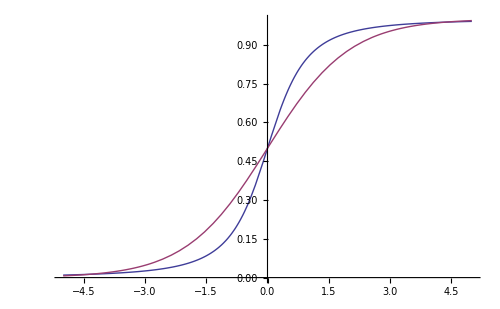

```mathematica
Plot[{sigma[t],sigmoid[t]}, {t,-5,5}, PlotLegend-> {Style["sigma", 16, FontFamily-> "Ubuntu"],Style["sigmoid",16,FontFamily-> "Ubuntu"]}, LegendPosition-> {1,0}, ImageSize-> 500, BaseStyle-> {FontSize-> 16, FontFamily-> "Ubuntu"}]
```